```mathematica
jmol2eVatom=0.0000103642688
```

0.0000103643

```mathematica
graphite[T_]:=-17368.441+170.73*T-24.3*T*Log[T]-0.4723*10^-3*T^2+2562600*T^(-1)-264300000*T^(-2)+1.2*10^10*T^(-3)
diamond[T_]:=-16359.441+175.61*T-24.31*T*Log[T]-0.4723*10^-3*T^2+2698000*T^(-1)-261000000*T^(-2)+1.11*10^10*T^(-3)
```

```mathematica
correction=jmol2eVatom*(graphite[T]-diamond[T])
```

0.0000103643 (-1009.+(9.×10^8)/T^3-3300000/T^2-135400/T-4.88 T+0.01 T Log[T])

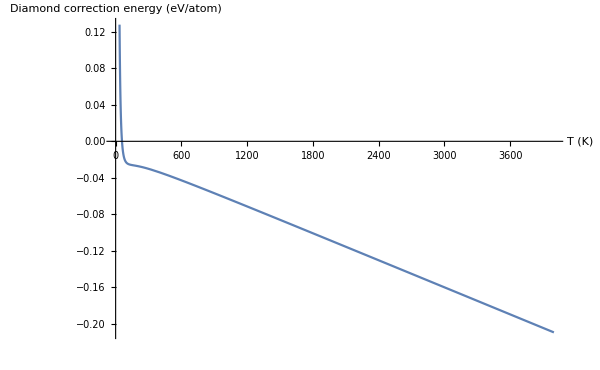

```mathematica
Plot[correction,{T,1,4000},AxesStyle->16,AxesLabel->{Style["T (K)",16],Style["Diamond correction energy (eV/atom)",16]},ImageSize->600]
```